(√(2/π) Sin[2 w])/w

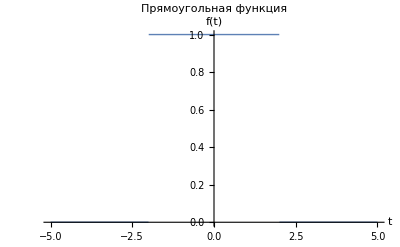

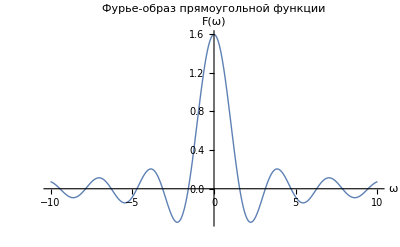

```mathematica
f[t_,a_,b_]:=Piecewise[{{a,Abs[t]≤b},{0,Abs[t]>b}}]

a=2;
b=2;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Прямоугольная функция", Exclusions->None]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ прямоугольной функции"]
```